```mathematica
(* Comparison between BE, MB and FE (quantum) statistics *)
```

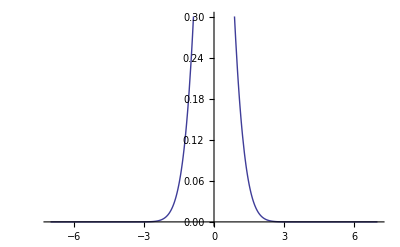

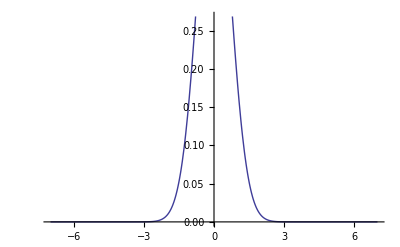

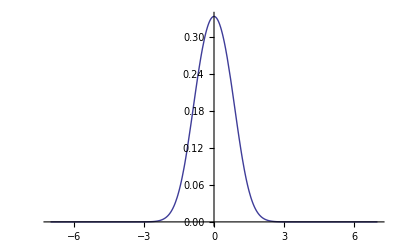

```mathematica
θ = -1;
z = 0.5;
Plot[1/((1/z)  Exp[c^2]-1),{c,-7,7}] (* BE *)
Plot[1/((1/z)  Exp[c^2]+0),{c,-7,7}] (* MB *)
Plot[1/((1/z)  Exp[c^2]+1),{c,-7,7}](* FD *)
```

```mathematica
NIntegrate[1/((1/z)  Exp[c^2]-1),{c,-7,7}] (* BE *)
NIntegrate[1/((1/z)  Exp[c^2]+0),{c,-7,7}] (* MB *)
NIntegrate[1/((1/z)  Exp[c^2]+1),{c,-7,7}](* FD *)
```

1.42882

0.886227

0.662459